# Name: John Wesley Hayhurst

## Mathematica Activity Due Friday, January 29th at the beginning of class. Your final file will be uploaded to Scholar.

## Objective: The objective of this activity is to learn how to use Mathematica to graph slope fields and solutions corresponding to differential equations, and to solve differential equations and initial value problems.

## Solving a Differential Equation in Mathematica

### Mathematica has many powerful features, including its ability to solve differential equations. The “DSolve” command automatically chooses the correct method to solve a differential equation. First, we will store a function into Mathematica. To store the function, click next to the text in the yellow box and hit “shift+Enter.”

```mathematica
f[x_,y_]=y[x]/x
(*Note that there is an underscore after each of the variables and square brackets following the function name.  We also indicate that y is a function of x by writing y[x] (not just y). *)
```

y[x]/x

### Now, we will have Mathematica solve the differential equation: dy/dx=y/x and give us the general solution. To solve, click next to the text in the yellow box and hit “shift+Enter.”

```mathematica
DSolve[y'[x]==f[x,y],y[x],x] (*The DSolve command solves the differential equation.  Note the capitalization for DSolve, the double equal signs and that the command requires three inputs--1. the differential equation, 2. the function for which you are solving and 3. the dependent variable*)
```

{{y[x]→x C[1]}}

### C[1] is any constant. Be very careful--Mathematica will not always give you the singular solutions, you will need to find those on your own. To solve an initial value problem for the differential equation and find the specific C[1], we modify the input. To see the particular solution whose initial condition is given by y(3)=2, click next to the text in the yellow box and hit “shift+Enter.”

```mathematica
DSolve[{y'[x]==f[x,y],y[3]==2},y[x],x] (*Note that there are now curly brackets around the differential equation and we list the initial conditions.*)
```

{{y[x]→(2 x)/3}}

### Now you try: 1. Suppose you have the first order differential equation: dy/dx=-xy^2. Store the righthand side as a new function g(x,y), find the general solution, and the particular solution given the initial conditions y(1)=1.

```mathematica
g[x_,y_] = -x*y[x]^2
```

-x y[x]^2

```mathematica
DSolve[y'[x]==g[x,y],y[x],x]
```

{{y[x]→2/(x^2-2 C[1])}}

```mathematica
DSolve[{y'[x]== g[x,y],y[1]==1},y[x],x]
```

{{y[x]→2/(1+x^2)}}

### Complete by hand to turn in: Use separation of variables to confirm the answer that Mathematica gave you. Be sure to include any singular solutions if they are not included in the general solution.

### 2. Suppose you have the first order differential equation: dy/dx=6(x(y-1))^(2/3). Store the righthand side as a new function g(x,y), find the general solution.

```mathematica
g[x_,y_] = 6*x*(y[x] -1)^(2/3)
```

6 x (-1+y[x])^(2/3)

```mathematica
DSolve[y'[x]==g[x,y],y[x],x]
```

{{y[x]→1/27 (27+27 x^6+27 x^4 C[1]+9 x^2 C[1]^2+C[1]^3)}}

### Complete by hand to turn in: Use separation of variables to confirm the answer that Mathematica gave you. Be sure to include any singular solutions if they are not included in the general solution.

### 3. Suppose you have the third order differential equation: y'''+4y''-5y'=0. We do not yet know how to solve this differential equation by hand. Use Mathematica to find the general solution and the particular solution given the initial conditions: y(0)=4, y'(0)=-7, and y''(0)=23. (To include multiple initial conditions, separate each condition by a comma within the curly brackets.)

```mathematica
g[x_,y_] = -4*y''[x] + 5*y'[x]
```

5 y'[x]-4 y''[x]

```mathematica
DSolve[{y'''[x]==g[x,y],y[0]==4,y'[0]==-7,y''[0]==23},y[x],x]
```

{{y[x]→-ⅇ^(-5 x) (-1-5 ⅇ^(5 x)+2 ⅇ^(6 x))}}

## Slope Fields

### Mathematica can also draw slope fields for us, which is really handy since they are tedious to do by hand! Let’s go back to our first example: dy/dx=y/x. To create the slope field, click next to the text in the yellow box and hit “shift+Enter.”

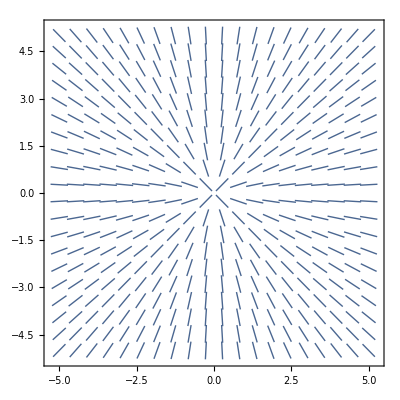

```mathematica
VectorPlot[{x,y},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20] (*The command VectorPlot has lots of parts.  For most applications, you only need to pay attention to the first three items in brackets.  If we think of dy/dx as a slope, so dy/dx=rise/run, the first set of curly brackets indicates the {run, rise}.  So for us, the run is x and the rise is 1.  The second two items in curly brackets give the domain and range for the slope field. *)
```

### We also know that the particular solution to the initial value problem whose initial condition is given by y(3)=2 is y=(2x)/3. To graph a particular solution, click next to the text in the yellow box and hit “shift+Enter.”

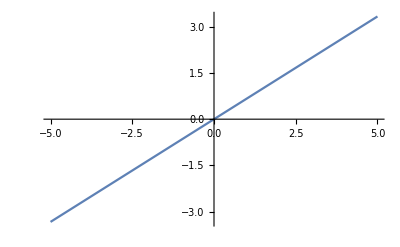

```mathematica
Plot[2x/3,{x,-5,5}] (*For Plot, the second portion (in curly brackets) gives the variable and its domain*)
```

### We can combine our slope field and this particular solution by using the “Show” command. To graph both the particular solution and the slope field, click next to the text in the yellow box and hit “shift+Enter.”

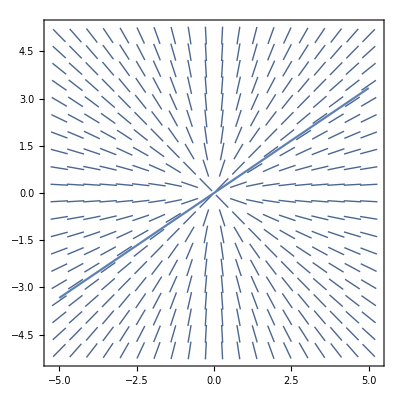

```mathematica
Show[VectorPlot[{x,y},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20],Plot[2x/3,{x,-5,5}] ] (*The command for VectorPlot and Plot are separated by a comma witin the Show command.*)
```

### We can modify our slope field to automatically draw in several solutions so that we may better understand the behavior of solutions. To see the slope field and many solutions, click next to the text in the yellow box and hit “shift+Enter.”

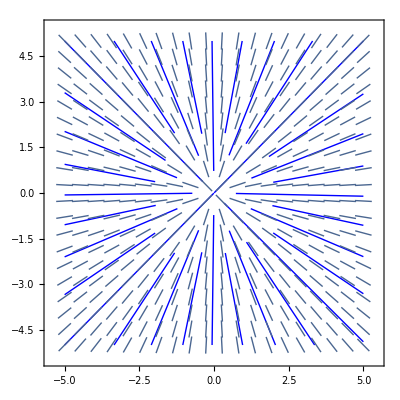

```mathematica
VectorPlot[{x,y},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20, StreamStyle->{Blue, Thick, "Line"}, StreamScale->Full, StreamPoints->Coarse]  (*We add information about the "stream" to see how the solution curves look.  Note that the solutions are not complete.*)
```

### Note that for this particular question, all of our solutions are lines passing through the origin.

### Complete by hand to turn in: Use the Theorem of Existance and Uniqueness to show that the differential equation dy/dx=y/x has unique solutions for y(a)=b when a and b are nonzero.

### Now you try: 1. Let’s go back to the first order differential equation: dy/dx=-xy^2. Create a slope field for the differential equation. (Note that -xy^2=-xy^2/1, so we can take the rise to be -xy^2 and the run to be 1.)

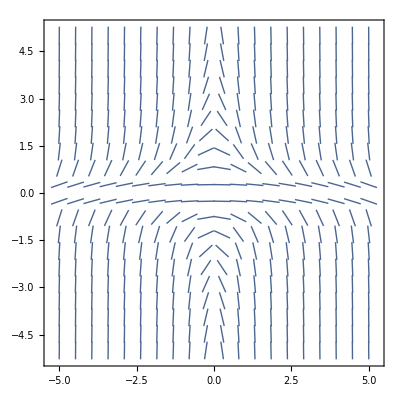

```mathematica
VectorPlot[{1,-x*y^2},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20]
```

### 3. Plot the slope field for the differential equation: dy/dx=-xy^2 along with the particular solution corresponding to the initial value problem given by y(1)=1on the same plot.

```mathematica
f[x_,y_]= -x*y[x]^2
```

-x y[x]^2

```mathematica
DSolve[{y'[x]==f[x,y],y[1]==1},y[x],x]
```

{{y[x]→2/(1+x^2)}}

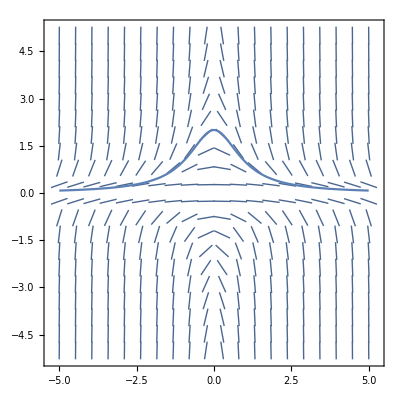

```mathematica
Show[VectorPlot[{1,-x*y^2},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20] ,Plot[2/(1+x^2),{x,-5,5}]]
```

### 4. Plot the slope field for the differential equation: dy/dx=-xy^2 along with several solution curves

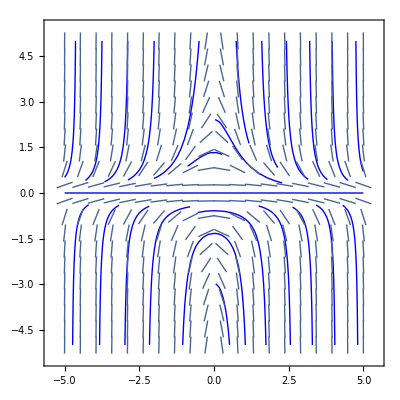

```mathematica
VectorPlot[{1,-x*y^2},{x,-5,5},{y,-5,5},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},VectorPoints->20, StreamStyle->{Blue, Thick, "Line"}, StreamScale->Full, StreamPoints->Coarse]
```

## Newton’s Law of Cooling

### On Monday, we looked at the differential equation associated with Newton’s Law of Cooling: dT/dt=k(A-T), where T(t) represents the temperature of a body at time t, which is immersed in a medium with constant temperature A, and k is constant rate of cooling. 1. Use Mathematica to solve for the general solution to Newton’s Law of Cooling (leave the generic constants A and k). 2. Use Mathematica to find the A and k corresponding to Monday’s assignment and to confirm that your particular solution is correct. You may find the “Solve” command useful. Information about the “Solve” command may be found at: https://reference.wolfram.com/language/ref/Solve.html 3. Plug in the values for A and k from Monday’s assignment into the differential equation. Then use Mathematica to create a slope field and several several solution curves. You will answer the questions below based on your slope field.

```mathematica
f[t_,T_]=k(A-T[t])
```

k (A-T[t])

```mathematica
DSolve[T'[t]==f[t,T],T[t],t]
```

{{T[t]→A+ⅇ^(-k t) C[1]}}

```mathematica
Solve[A+ⅇ^(-k *0) 24.6 == 94.6,{A}]
```

{{A→70.}}

```mathematica
Solve[70+ⅇ^(-k *1) 24.6 == 93.4, {k}]
```

{{k→0.0500104}}

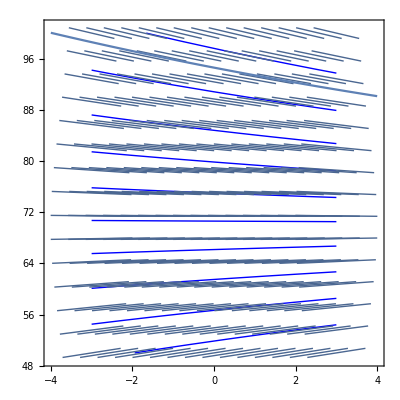

```mathematica
Show[VectorPlot[{1,0.0500104*(70-T)},{t,-3,3},{T,50,100},VectorStyle->Arrowheads[0],Axes->True,VectorScale->{Tiny,Automatic,None},StreamStyle->{Blue, Thick, "Line"}, StreamScale->Full, StreamPoints->Coarse],
Plot[70+ⅇ^(-0.0500104t)24.6,{t,-4,4}]]
```

### Suppose that T(0)>70. Describe the behavior of your solutions (in particular, the limit as time approaches infinity).

Supposing the T(0) > 70 the solution as time approaches infinity the temperature will decrease so that it will eventually reach A which in this case is 70. The limit as time approaches infinity is 70

### Suppose that T(0)<70. Describe the behavior of your solutions (in particular, the limit as time approaches infinity).

Supposing the T(0) < 70 the solution as time approaches infinity the temperature will increase so that it will eventually reach A which in this case is 70. The limit as time approaches infinity is 70

### Suppose that T(0)=70. Describe the behavior of your solutions (in particular, the limit as time approaches infinity).

Supposing that T(0) = 70 the solution as time approaches infinity the temperature will stay the same so that it will stay at A which in this case is 70. The limit as time approaches infinity is 70